# 2 edges -Graphics-

## |z_1⟩ = |z⟩ |ω_1⟩ = |ω⟩ |z_2⟩ = ⅇ^(ⅈ θ) |z] |ω_2⟩ = ⅇ^(ⅈ φ) |ω]

```mathematica
Quit
```

```mathematica
ResourceFunction["MaTeXInstall"][];
<<MaTeX`
```

## Modules:

```mathematica
Main module;
```

```mathematica
main[parameters_]:=Module[{array=parameters},
{xmin, xmax}={array[["xmin"]], array[["xmax"]]};
{γ,λ}={array[["γ"]], array[["λ"]]};
{z00,z10,ω00,ω10,θ0,φ0}={array[["z0"]],array[["z1"]] ,array[["ω0"]],array[["ω1"]],array[["θ"]],array[["φ"]]};
ndsolvemethod=array[["method"]];

Differential equations;
eq1= z0'[t]==-ⅈ (Abs[ω0[t]]^2 + Abs[ω1[t]]^2)(λ + 2 γ* ⅇ^(-ⅈ (θ[t]+φ[t])*))z0[t];
eq2= z1'[t]==-ⅈ (Abs[ω0[t]]^2 + Abs[ω1[t]]^2)(λ + 2 γ* ⅇ^(-ⅈ (θ[t]+φ[t])*))z1[t];
eq3= ω0'[t]==-ⅈ(Abs[z0[t]]^2 + Abs[z1[t]]^2)(λ + 2γ* ⅇ^(-ⅈ (θ[t]+φ[t])*))ω0[t];
eq4= ω1'[t]==-ⅈ(Abs[z0[t]]^2 + Abs[z1[t]]^2)(λ + 2γ* ⅇ^(-ⅈ (θ[t]+φ[t])*))ω1[t];
eq5= θ'[t]== -2(Abs[ω0[t]]^2 + Abs[ω1[t]]^2)(λ+2 Re[γ* ⅇ^(-ⅈ(θ[t]+φ[t])*)]);
eq6= φ'[t]== -2(Abs[z0[t]]^2 + Abs[z1[t]]^2)(λ+2 Re[γ* ⅇ^(-ⅈ(θ[t]+φ[t])*)]);

soluz0=NDSolve[{eq1,eq2, eq3, eq4, eq5, eq6, z0[0]==z00, z1[0]==z10, ω0[0]==ω00, ω1[0]==ω10, θ[0]==θ0, φ[0]==φ0}, z0,{t, xmin, xmax},Method-> ndsolvemethod/._Missing-> "Automatic"];
soluz1=NDSolve[{eq1,eq2, eq3, eq4, eq5, eq6, z0[0]==z00, z1[0]==z10, ω0[0]==ω00, ω1[0]==ω10, θ[0]==θ0, φ[0]==φ0}, z1,{t, xmin, xmax},Method-> ndsolvemethod/._Missing-> "Automatic"];
soluω0=NDSolve[{eq1,eq2, eq3, eq4, eq5, eq6, z0[0]==z00, z1[0]==z10, ω0[0]==ω00, ω1[0]==ω10, θ[0]==θ0, φ[0]==φ0}, ω0,{t, xmin, xmax},Method-> ndsolvemethod/._Missing-> "Automatic"];
soluω1=NDSolve[{eq1,eq2, eq3, eq4, eq5, eq6, z0[0]==z00, z1[0]==z10, ω0[0]==ω00, ω1[0]==ω10, θ[0]==θ0, φ[0]==φ0}, ω1,{t, xmin, xmax},Method-> ndsolvemethod/._Missing-> "Automatic"];
soluθ=NDSolve[{eq1,eq2,eq3, eq4, eq5, eq6, z0[0]==z00, z1[0]==z10, ω0[0]==ω00, ω1[0]==ω10, θ[0]==θ0, φ[0]==φ0}, θ,{t, xmin, xmax},Method-> ndsolvemethod/._Missing-> "Automatic"];
soluφ=NDSolve[{eq1,eq2, eq3, eq4, eq5, eq6, z0[0]==z00, z1[0]==z10, ω0[0]==ω00, ω1[0]==ω10, θ[0]==θ0, φ[0]==φ0}, φ,{t, xmin, xmax},Method-> ndsolvemethod/._Missing-> "Automatic"];

Matrices;
Eα[t_]={{Abs[z0[t]/.soluz0]^2 + Abs[z1[t]/.soluz1]^2,0},
	  {0,(Abs[z0[t]/.soluz0]^2 + Abs[z1[t]/.soluz1]^2)ⅇ^(-ⅈ ((θ[t]/.soluθ)*-(θ[t]/.soluθ)))}};
Eβ[t_]={{Abs[ω0[t]/.soluω0]^2 + Abs[ω1[t]/.soluω1]^2,0},
	    {0,(Abs[ω0[t]/.soluω0]^2 + Abs[ω1[t]/.soluω1]^2)ⅇ^(-ⅈ ((φ[t]/.soluφ)*-(φ[t]/.soluφ)))}};

Fcα[t_]={{0,ⅇ^(-ⅈ (θ[t]/.soluθ)*)(Abs[z0[t]/.soluz0]^2 + Abs[z1[t]/.soluz1]^2)},
	      {-ⅇ^(-ⅈ (θ[t]/.soluθ)*)(Abs[z0[t]/.soluz0]^2 + Abs[z1[t]/.soluz1]^2),0}};
Fcβ[t_]={{0,ⅇ^(-ⅈ (φ[t]/.soluφ)*)(Abs[ω0[t]/.soluω0]^2 + Abs[ω1[t]/.soluω1]^2)},
	      {-ⅇ^(-ⅈ (φ[t]/.soluφ)*)(Abs[ω0[t]/.soluω0]^2 + Abs[ω1[t]/.soluω1]^2),0}};

Fα[t_]=Fcα[t]*;
Fβ[t_]=Fcβ[t]*;

e[t_]= ∑_(i=1)^2 (∑_(j=1)^2 (Eα[t][[i,j]]Eβ[t][[i,j]]));
f[t_]=  ∑_(i=1)^2 (∑_(j=1)^2 (Fα[t][[i,j]]Fβ[t][[i,j]]));
fc[t_]= ∑_(i=1)^2 (∑_(j=1)^2 (Fcα[t][[i,j]]Fcβ[t][[i,j]]));
H[t_]= λ e[t]+γ f[t]+γ* fc[t];

Quadrupole and volume;
σ[1]={{0,1},{1,0}};
σ[2]={{0,-ⅈ},{ⅈ,0}};
σ[3]={{1,0},{0,-1}};

z[1]={z0[t],z1[t]};
z[2]={-(z1[t])* ⅇ^(ⅈ θ[t]),(z0[t])* ⅇ^(ⅈ θ[t])};

solutions=Flatten[{soluz0,soluz1,soluθ}];

quadrupole[t_,a_,b_]=1/2 Sum[((z[k]*.σ[a].z[k]) (z[k]*.σ[b]. z[k]))/(z[k]*.z[k]),{k,2}];

T[t_]={{quadrupole[t,1,1],quadrupole[t,1,2],quadrupole[t,1,3]},
	     {quadrupole[t,2,1],quadrupole[t,2,2],quadrupole[t,2,3]},
	     {quadrupole[t,3,1],quadrupole[t,3,2],quadrupole[t,3,3]}};

area[t_]=quadrupole[t,1,1]+quadrupole[t,2,2]+quadrupole[t,3,3];

volume1[t_]=((2/9)^2 1/16((z[1]* .z[1])(z[2]*. z[2]))/area[t] Det[T[t]] )^(1/4);

nor[1]={z[1]*.σ[1].z[1],z[1]*.σ[2].z[1],z[1]*.σ[3].z[1]};
nor[2]={z[2]*.σ[1].z[2],z[2]*.σ[2].z[2],z[2]*.σ[3].z[2]};

Angles;
angle[t_,a_,b_]=((nor[a]+nor[b]).(nor[a]+nor[b])-(z[a]* .z[a])^2-(z[b]* .z[b])^2)/(2 (z[a]* .z[a]) (z[b]* .z[b]));

Plots;
Spinors;
gr1 = Plot[{Abs[z0[t]/.soluz0],
	        Abs[z1[t]/.soluz1],
	        Abs[ω0[t]/.soluω0],
	        Abs[ω1[t]/.soluω1]}, {t,xmin,xmax},PlotLegends-> Placed[{MaTeX["|z^0|"], MaTeX["|z^1|"], MaTeX["|\\omega^0|"], MaTeX["|\\omega^1|"]}, Above],AxesLabel-> {MaTeX["t"]},ImageSize-> 300];

Areas;
gr2 = Plot[{Abs[z0[t]/.soluz0]^2+Abs[z1[t]/.soluz1]^2,
		 Abs[ω0[t]/.soluω0]^2+Abs[ω1[t]/.soluω1]^2}, {t,xmin,xmax},
AxesLabel->{MaTeX["t"],MaTeX["E^{\\alpha}"]},ImageSize-> 300];

Phases;
gr3 = Plot[{θ[t]/.soluθ,φ[t]/.soluφ}, {t,xmin,xmax},PlotLegends-> Placed[{MaTeX["\\theta"],MaTeX["\\varphi"]},Above],AxesLabel-> {MaTeX["t"],MaTeX["\\theta"]},ImageSize-> 300];

Closure constraint;
closure1=Abs[z0[t]/.soluz0]^2(1-ⅇ^(ⅈ((θ[t]/.soluθ)-(θ[t]/.soluθ)*)))+
		Abs[z1[t]/.soluz1]^2(1-ⅇ^(ⅈ((θ[t]/.soluθ)-(θ[t]/.soluθ)*)));
closure2=(z0[t]/.soluz0 )(z1[t]/.soluz1)*(1-ⅇ^(ⅈ((θ[t]/.soluθ)-(θ[t]/.soluθ)*)));
gr4 = Plot[{Abs[closure1], Abs[closure2]}, {t,xmin,xmax},PlotLegends-> Placed[{MaTeX["\\text{Closure 1}"], MaTeX["\\text{Closure 2}"]},Above],AxesLabel-> {MaTeX["t"]},ImageSize->300];

Hamiltonian;
gr5=Plot[{Abs[H[t]],Re[H[t]],Im[H[t]]}, {t,xmin,xmax},PlotLegends-> Placed[{MaTeX["|H|"],MaTeX["\\text{Re}(H)"], MaTeX["\\text{Im}(H)"]},Above],PlotRange-> All,AxesLabel-> {MaTeX["t"]},ImageSize->300];

Quadrupole and volume;
gr6 = Table[Plot[Abs[quadrupole[t,i,j]/.solutions],{t,xmin,xmax},AxesLabel-> {MaTeX["t"]}],{i,3},{j,3}]//TableForm;
gr7 = Plot[{volume1[t]/.solutions},{t,xmin,xmax},PlotRange-> All,AxesLabel-> {MaTeX["t"],MaTeX["\\text{Volume}"]}];

<|"spinors"-> gr1,"E"-> gr2,"phases"-> gr3, "closure"-> gr4, "H"-> gr5, "quad"-> gr6,"vol"-> gr7|>

];

Calculate λ from γ and H;
initialvalues[parameters_]:=Module[{array=parameters},
{γ,H0}={array[["γ"]],array["H0"]};
{z00,z10,ω00,ω10,θ0,φ0}={array[["z0"]],array[["z1"]] ,array[["ω0"]],array[["ω1"]],array[["θ"]],array[["φ"]]};

Eα0={{Abs[z00]^2 + Abs[z10]^2,0},
	{0,(Abs[z00]^2 + Abs[z10]^2)ⅇ^(-ⅈ (θ0*-θ0))}};
Eβ0={{Abs[ω00]^2 + Abs[ω10]^2,0},
	{0,(Abs[ω00]^2 + Abs[ω10]^2)ⅇ^(-ⅈ (φ0*-φ0))}};

Fcα0={{0,ⅇ^(-ⅈ θ0*)(Abs[z00]^2 + Abs[z10]^2)},
	      {-ⅇ^(-ⅈ θ0*)(Abs[z00]^2 + Abs[z10]^2),0}};
Fcβ0={{0,ⅇ^(-ⅈ φ0*)(Abs[ω00]^2 + Abs[ω10]^2)},
	      {-ⅇ^(-ⅈ φ0*)(Abs[ω00]^2 + Abs[ω10]^2),0}};

Fα0=Fcα0*;
Fβ0=Fcβ0*;

e0= ∑_(i=1)^2 (∑_(j=1)^2 Eα0[[i,j]]Eβ0[[i,j]]);
f0=  ∑_(i=1)^2 (∑_(j=1)^2 Fα0[[i,j]]Fβ0[[i,j]]);
fc0=∑_(i=1)^2 (∑_(j=1)^2 Fcα0[[i,j]]Fcβ0[[i,j]]);

λ = (H0-γ* fc0-γ f0)/e0;

<|"λ"-> λ, "e0"-> e0, "f0"-> f0, "fc0"-> fc0|>

];

Plot the results;
plot[parameters_]:=Module[{array=parameters},
params=array;

If[params[["λ"]]==None,
     params[["λ"]]=initialvalues[params][["λ"]]];

allplots=main[params];

Print[MaTeX["\\text{Evolution of the variables:}"]];
Print[Style[Row[{allplots[["spinors"]],allplots[["phases"]],allplots[["E"]],allplots[["vol"]]}], ImageSizeMultipliers->{1,1}]];

Print[MaTeX["\\text{Consistency checks:}"]];
Print[Style[Row[{allplots[["closure"]],allplots[["H"]]}], ImageSizeMultipliers->{1,1}]];

Print[MaTeX["\\text{Evolution of the quadrupole:}"]];
Print[allplots[["quad"]]];
];
```

## Plots

If we set the value of λ to None, then λ will be determined from the values of γ and H. If we give a value to λ, then H will be determined from γ and λ.

### Oscillatory

-Graphics-

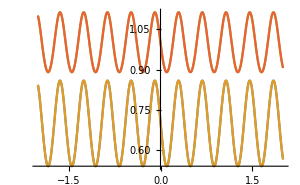
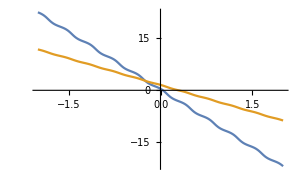
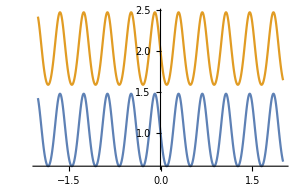
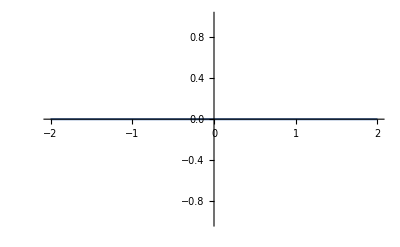

-Graphics-

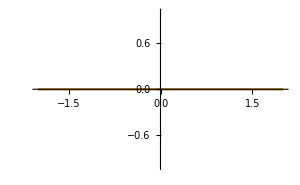
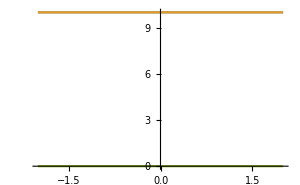

-Graphics-

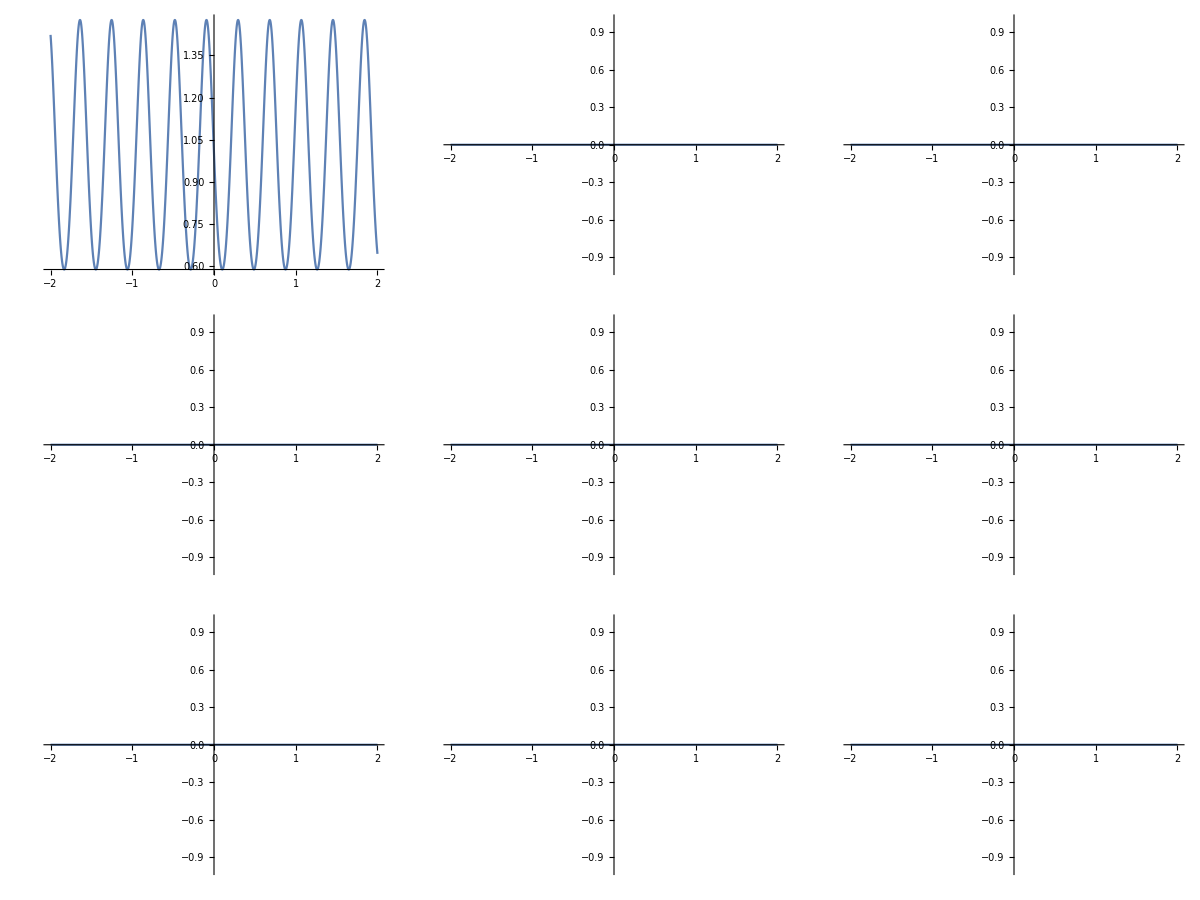

```mathematica
params=<|"xmin"-> -2,"xmax"-> 2,(*Minimum and maximum values of t*)
	      "γ"-> 1,"H0"-> 10,"λ"-> None,(*Coupling constants and Hamiltonian*)
	      "z0"-> 1/Sqrt[2],"z1"-> 1/Sqrt[2],"ω0"-> 1,"ω1"->1,(*Initial values of the spinors*)
	      "θ"->π/7,"φ"-> π/2,(*Initial values of the phases*)
	      "method"-> "Automatic" (*In case we want to use a specific method to solve the differential equations*)|>;

allplots=plot[params]
```

### Divergent

In the divergent regimes, we will have singularities for some values of t, so Mathematica will extrapolate the values out of these boundaries. Therefore, once we see where the divergences are, we can change xmin and xmax so that we remain inside the safe zone.

-Graphics-

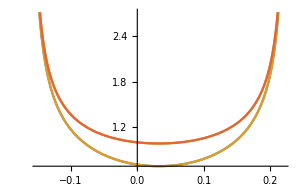
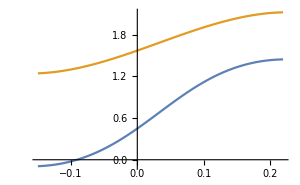
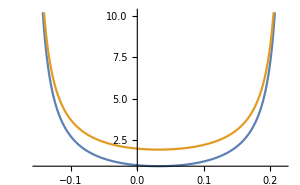
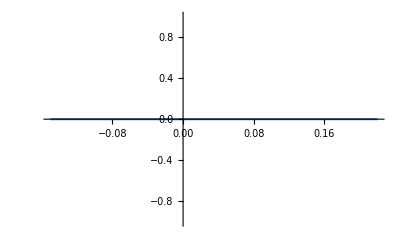

-Graphics-

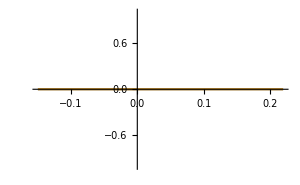
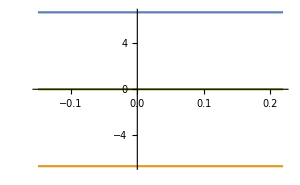

-Graphics-

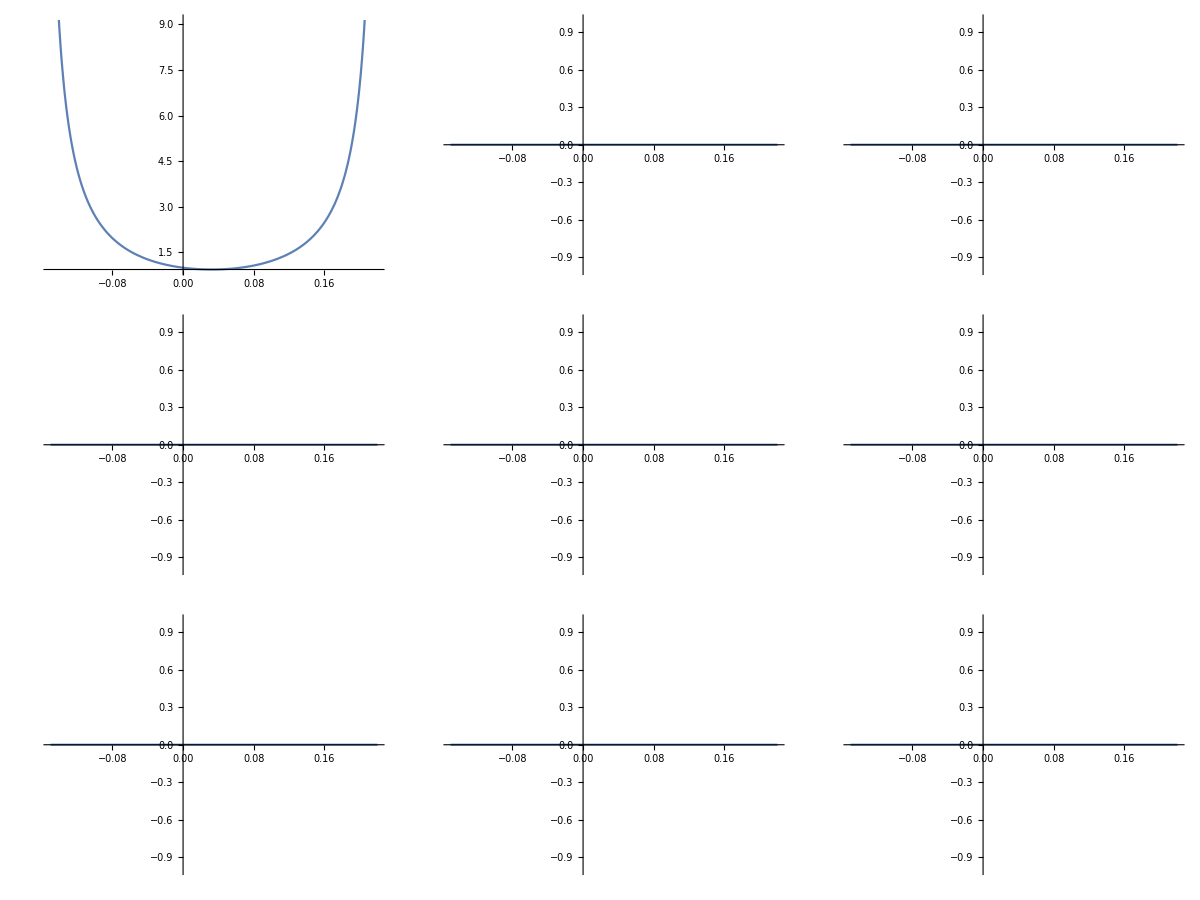

```mathematica
params=<|"xmin"-> -0.15,"xmax"-> 0.22,
	      "γ"-> 1+ⅈ,"H0"-> 0,"λ"-> 1,
	   "z0"-> 1/Sqrt[2],"z1"-> 1/Sqrt[2],"ω0"-> 1,"ω1"->1,
	       "θ"->π/7,"φ"-> π/2,
	       "method"-> "Automatic"|>;

allplots=plot[params]
```